# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pcs/Desktop/Breaking time reversal symmetry/Generalized kicks

```mathematica
LaunchKernels[8]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=Sz[J]=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=Sx[J]=SparseArray[(1/2)(SM[J]+Sm[J])];
Sy[J_]:=Sy[J]=SparseArray[(1/(2I))(SM[J]-Sm[J])];
```

# Method

```mathematica
radius=1.99999;
delta=0.050;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20272

5216

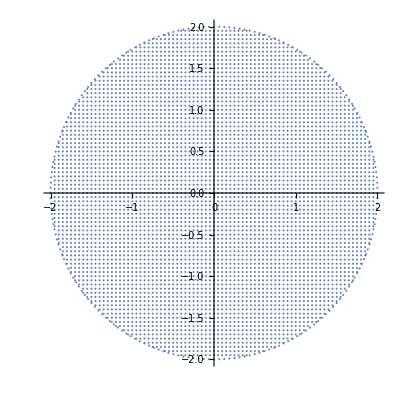

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
(*rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];*)
```

```mathematica
Clear[J];
J=200;
α=0.84;
τ=1;
k=20.;
```

```mathematica
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a1,a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Quiet[Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]]
];
a1[J_Integer,theta_,phi_]:=Module[{mvals=Range[-J,J],coeffs},
Quiet[Normalize[N[Table[Binomial[2J,J+m]*(Cos[theta/2]^(J+m))*(Exp[I*phi]Sin[theta/2])^(J-m),{m,mvals}]]]]
];
```

```mathematica
flist={};
Do[
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
AppendTo[flist,neweigenvec];
,{k,10,20,0.1}];
```

```mathematica
AbsoluteTiming[coherentstates=Developer`ToPackedArray[ParallelTable[a2[J,i[[1]],i[[2]]],{i,region}]];]
```

{20.5135,Null}

```mathematica
Clear[iprvectorized];
iprvectorized[eigenvec_,states_]:=Module[{overlaps},
overlaps=Conjugate[eigenvec].Transpose[states];
Total[Abs[overlaps]^4,{1}]
];
```

```mathematica
AbsoluteTiming[iprdata=ParallelTable[iprvectorized[i,coherentstates],{i,flist}];]
```

{11.4828,Null}

```mathematica
plots=Table[ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],iprdata[[i]]}],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",ColorFunction->"TemperatureMap",ImageSize->800],{i,Length[flist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```